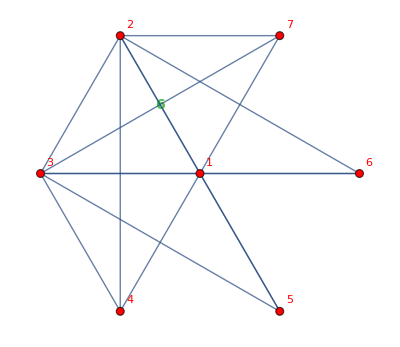
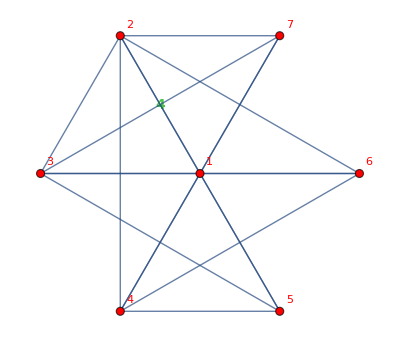
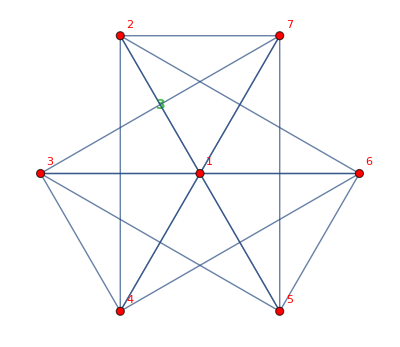
{{-Graphics-{15,15}},{-Graphics-{15,17}},{-Graphics-{15,18}}}

```mathematica
Map[With[{g=#},{Labeled[g,{VertexCount[g]*3-6,EdgeCount[g]}]}]&,BarelyFourColorableGraphsOfCount[7]]
```

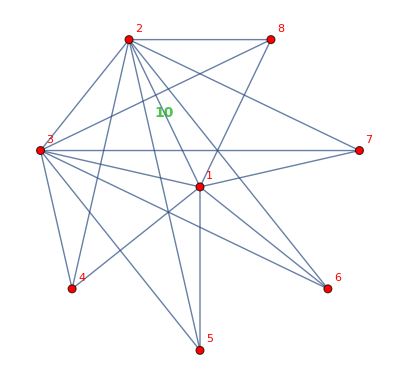
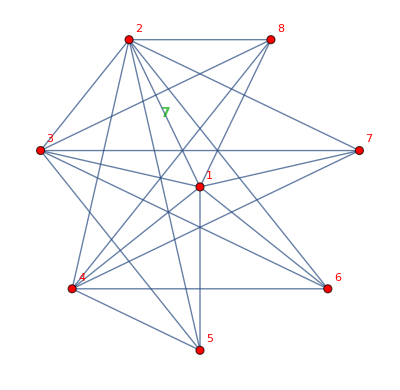
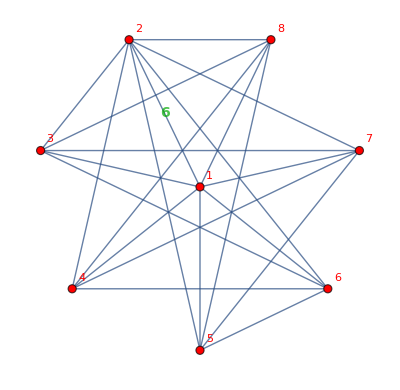
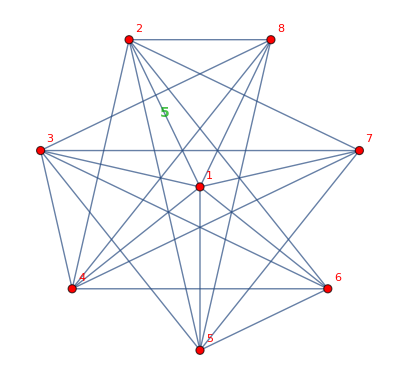
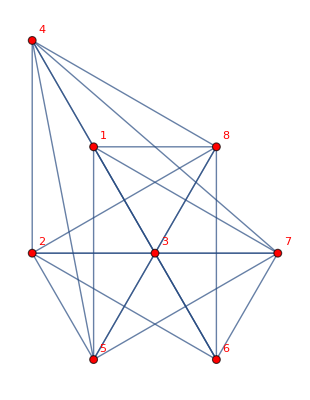
{{-Graphics-{18,18}},{-Graphics-{18,21}},{-Graphics-{18,22}},{-Graphics-{18,23}},{-Graphics-{18,24}}}

```mathematica
Map[With[{g=#},{Labeled[g,{VertexCount[g]*3-6,EdgeCount[g]}]}]&,BarelyFourColorableGraphsOfCount[8]]
```

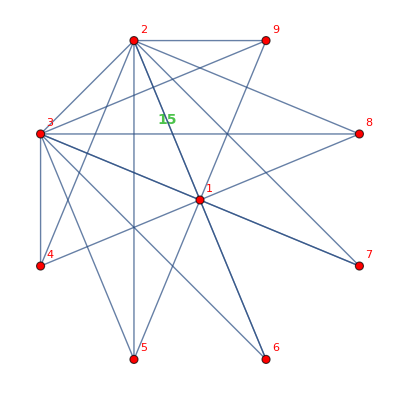
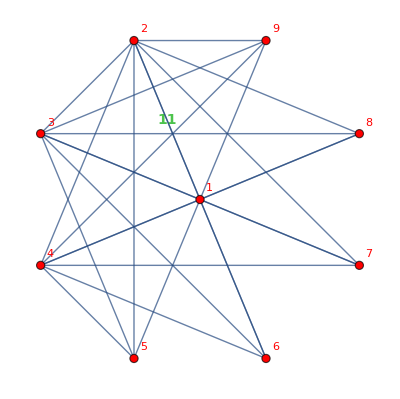
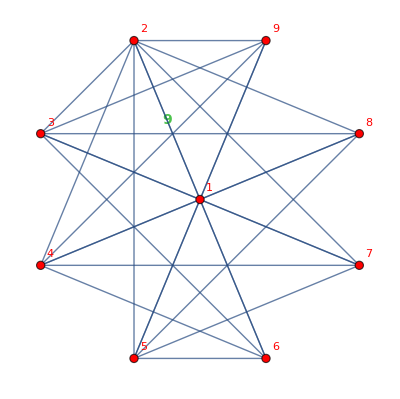
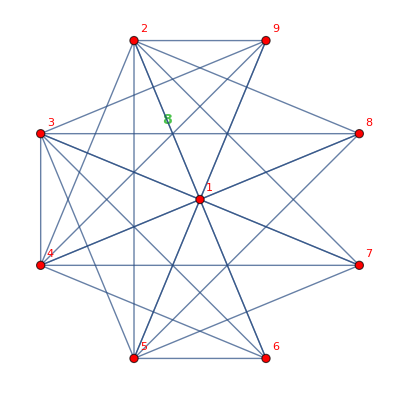
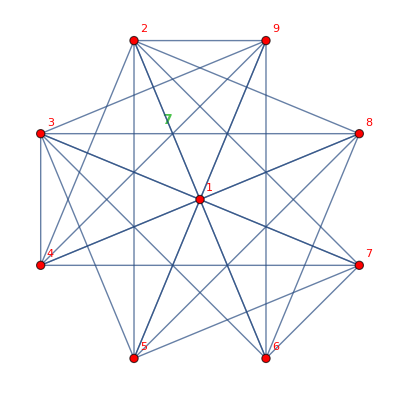
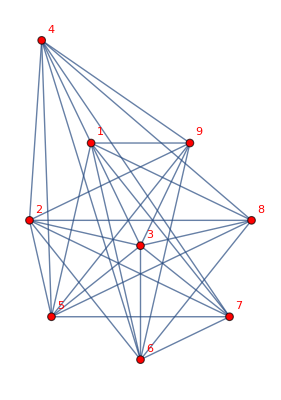
{{-Graphics-{21,21}},{-Graphics-{21,25}},{-Graphics-{21,27}},{-Graphics-{21,28}},{-Graphics-{21,29}},{-Graphics-{21,30}}}

```mathematica
Map[With[{g=#},{Labeled[g,{VertexCount[g]*3-6,EdgeCount[g]}]}]&,BarelyFourColorableGraphsOfCount[9]]
```

```mathematica
CompFromPart[10,{4,3,2,1}]
```

{{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4},{5<->6,5<->7,6<->7},{8<->9},{}}

```mathematica
IntegerPartitions[7,{4}]
```

{{4,1,1,1},{3,2,1,1},{2,2,2,1}}

```mathematica
EdgeCount[-Graphics-]
```

18

```mathematica
BarelyFourColorableGraphsOfCount2[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{4}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
g=CompleteGraph[count];
With[{h=
EdgeDelete[
CompleteGraph[count,
GraphLayout->"CircularEmbedding",
EdgeStyle->Map[#->{Thick,Red}&,comp],
EdgeLabels->First[EdgeList[g]]->Style[Framed[Length[comp],Background->White],Darker[Green],Bold,14],
VertexStyle->Red,
VertexLabels->"Name"
],
comp]},
Labeled[GraphComplement[h, EdgeStyle->Directive[Red,Thick]],{PartitionTypeLabel[Reverse [part]],Style[EdgeCount[h]-(VertexCount[h]*3-6),Bold],VertexCount[h]*3-6,EdgeCount[h]}]
]
,
{part, parts}
]
]
```

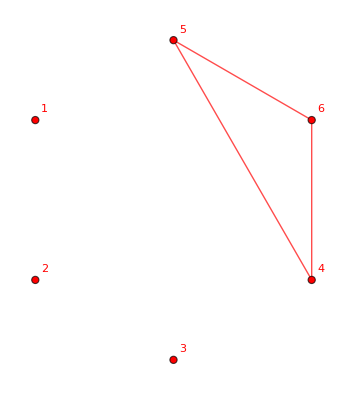
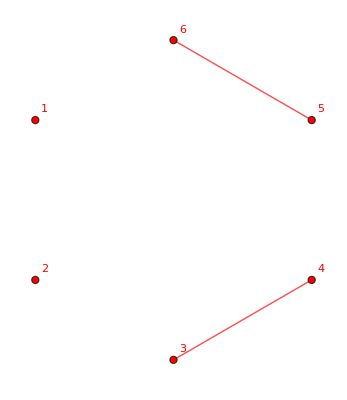
{-Graphics-{3111,0,12,12},-Graphics-{2211,1,12,13}}

```mathematica
BarelyFourColorableGraphsOfCount2[6]
```

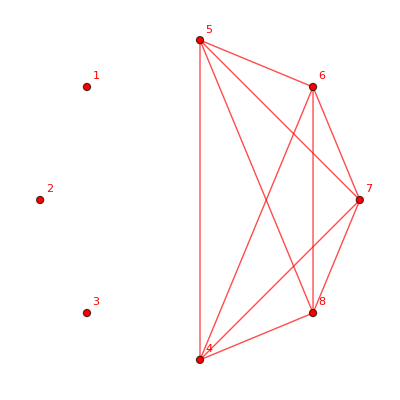
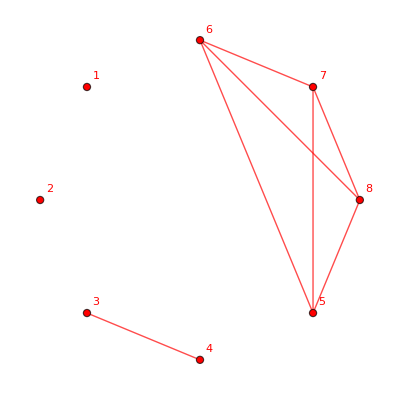
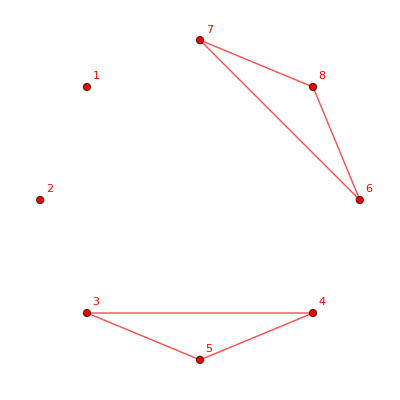
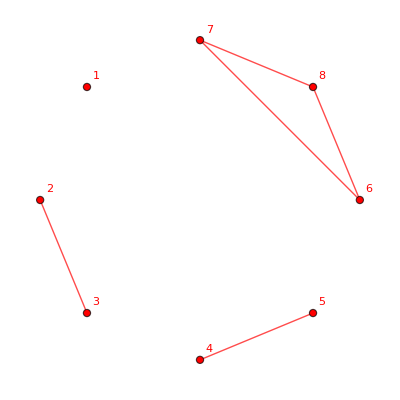
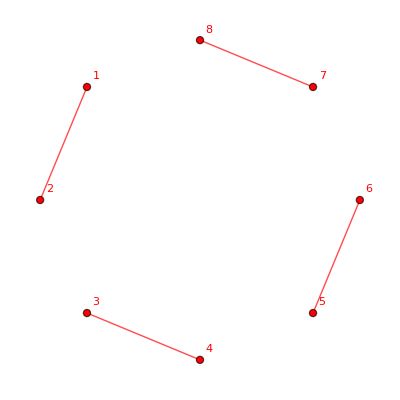
{-Graphics-{5111,0,18,18},-Graphics-{4211,3,18,21},-Graphics-{3311,4,18,22},-Graphics-{3221,5,18,23},-Graphics-{2222,6,18,24}}

```mathematica
BarelyFourColorableGraphsOfCount2[8]
```

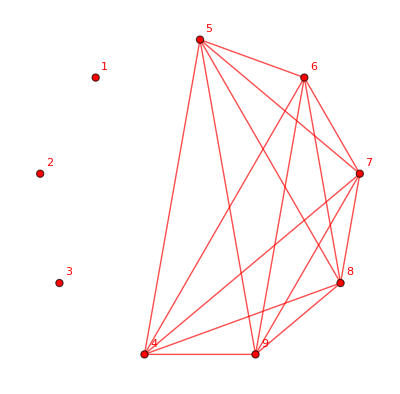
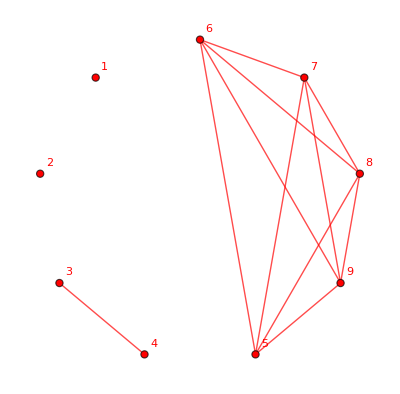
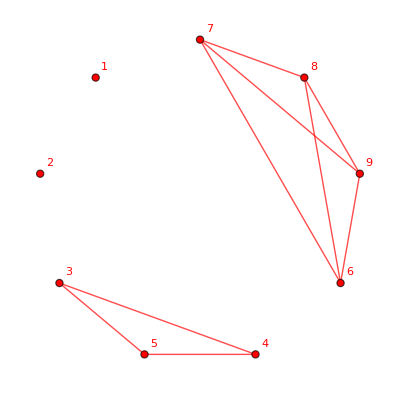
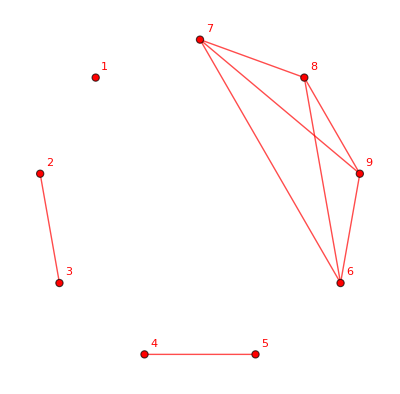
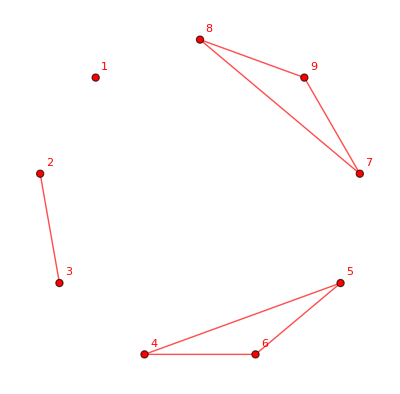
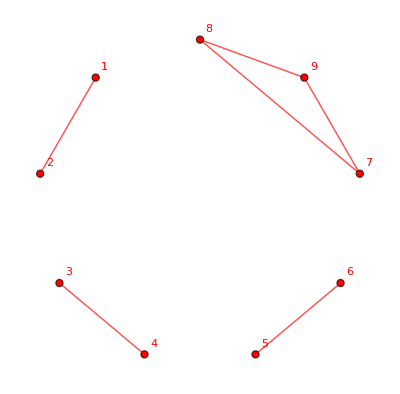
{-Graphics-{6111,0,21,21},-Graphics-{5211,4,21,25},-Graphics-{4311,6,21,27},-Graphics-{4221,7,21,28},-Graphics-{3321,8,21,29},-Graphics-{3222,9,21,30}}

```mathematica
BarelyFourColorableGraphsOfCount2[9]
```

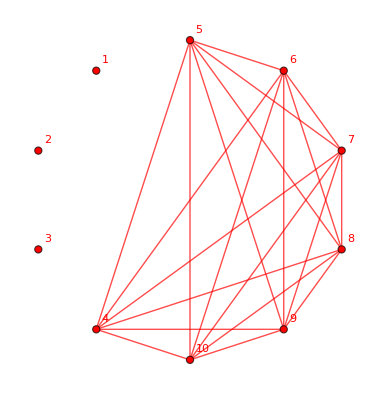
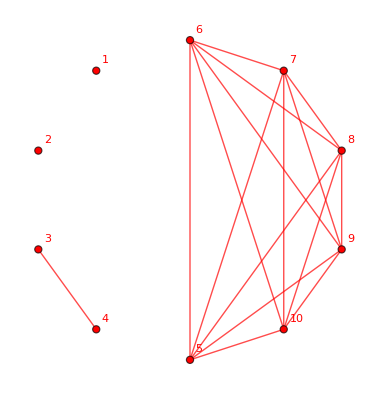
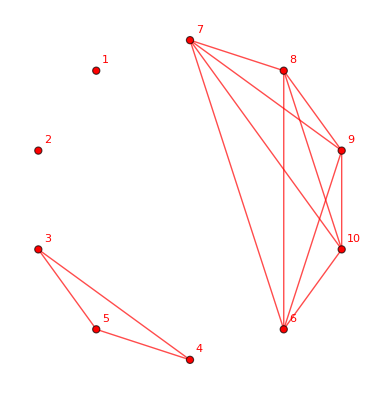
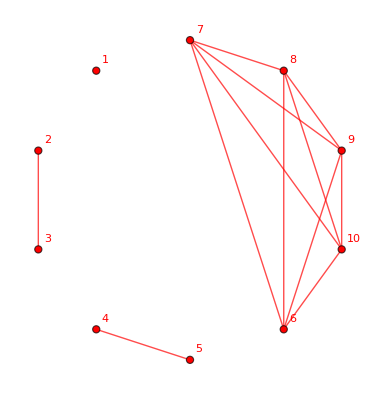
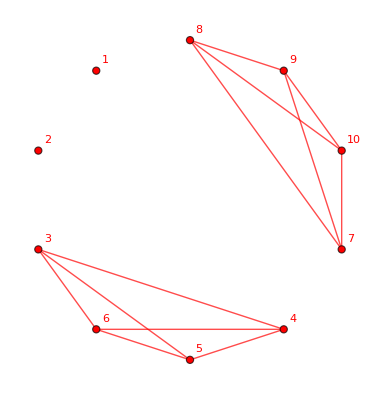
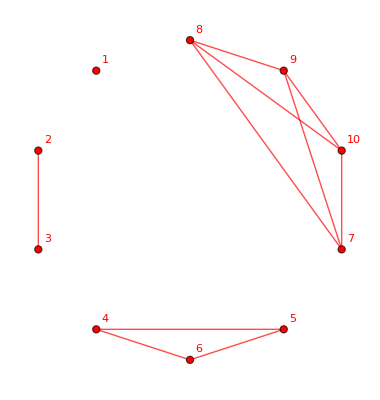
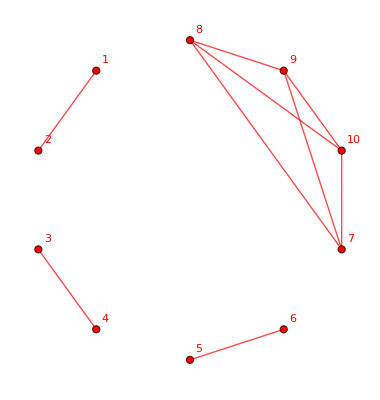
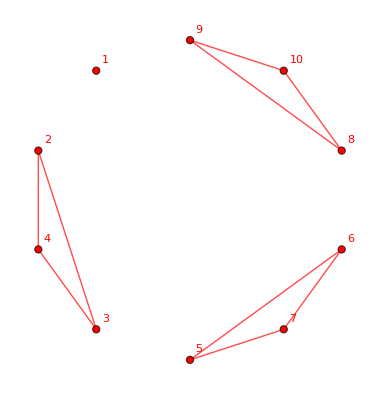
{-Graphics-{7111,0,24,24},-Graphics-{6211,5,24,29},-Graphics-{5311,8,24,32},-Graphics-{5221,9,24,33},-Graphics-{4411,9,24,33},-Graphics-{4321,11,24,35},-Graphics-{4222,12,24,36},-Graphics-{3331,12,24,36},-Graphics-{3322,13,24,37}}

```mathematica
BarelyFourColorableGraphsOfCount2[10]
```

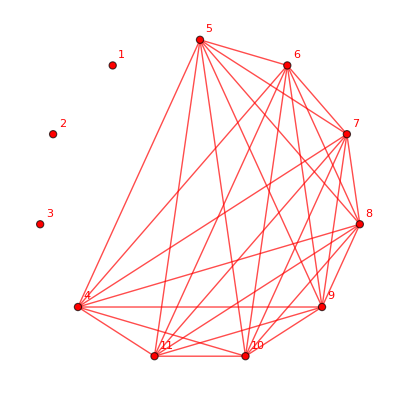
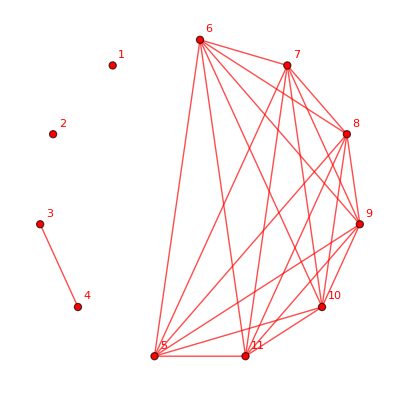
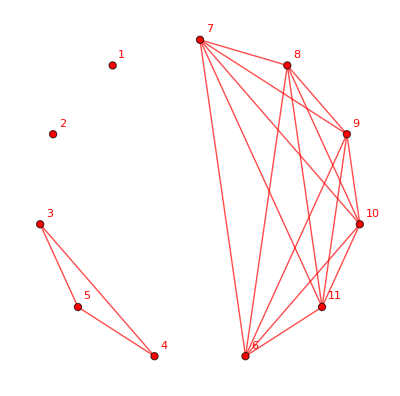
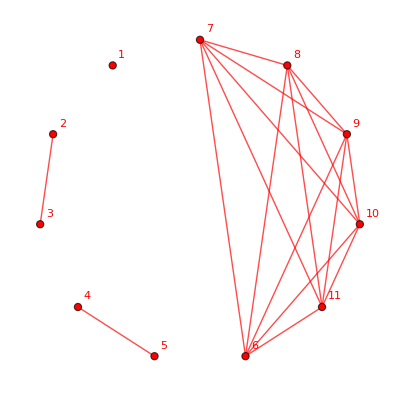
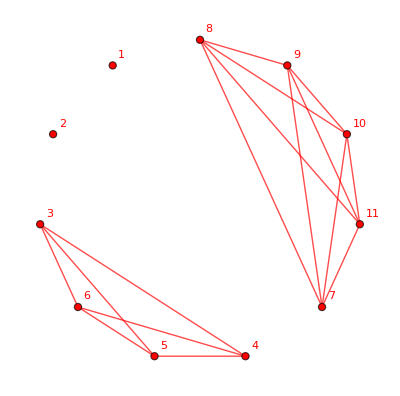
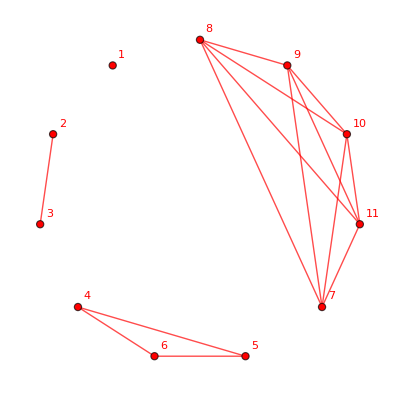
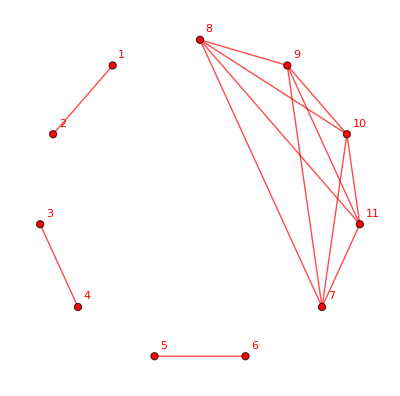
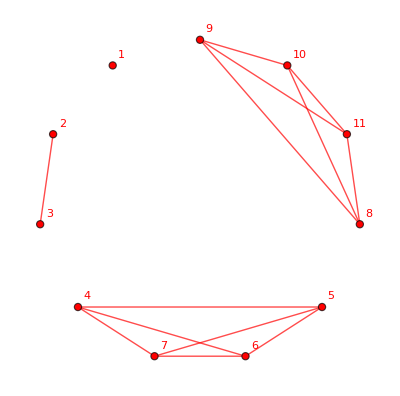
{-Graphics-{8111,0,27,27},-Graphics-{7211,6,27,33},-Graphics-{6311,10,27,37},-Graphics-{6221,11,27,38},-Graphics-{5411,12,27,39},-Graphics-{5321,14,27,41},-Graphics-{5222,15,27,42},-Graphics-{4421,15,27,42},-Graphics-{4331,16,27,43},-Graphics-{4322,17,27,44},-Graphics-{3332,18,27,45}}

```mathematica
BarelyFourColorableGraphsOfCount2[11]
```

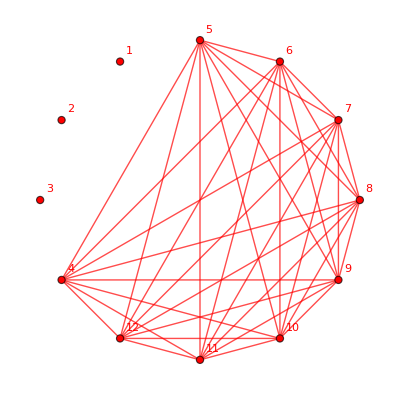
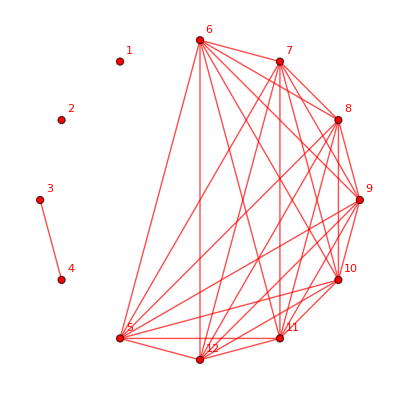
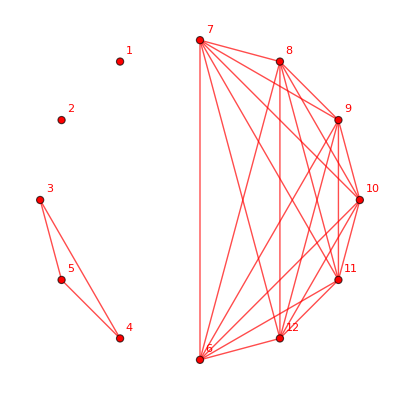
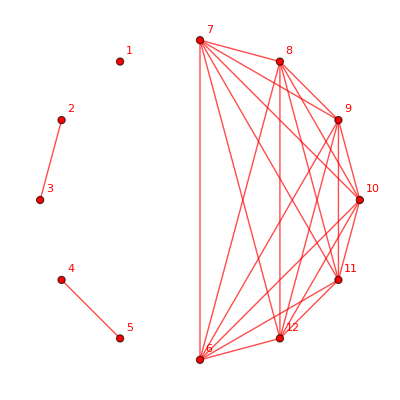
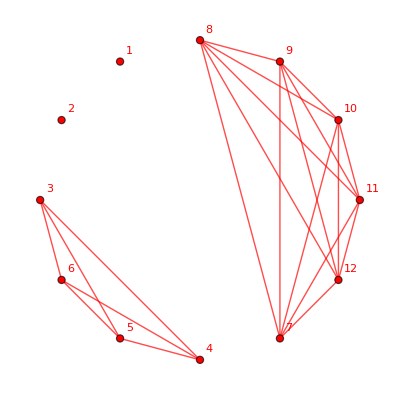
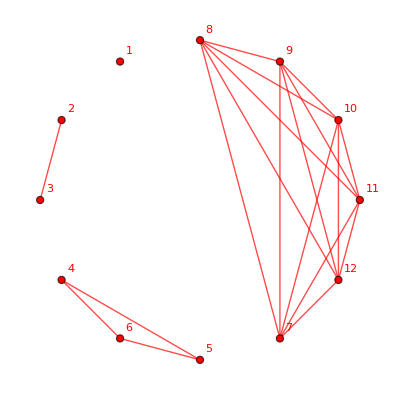
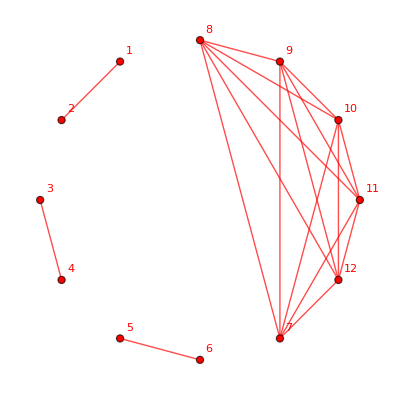
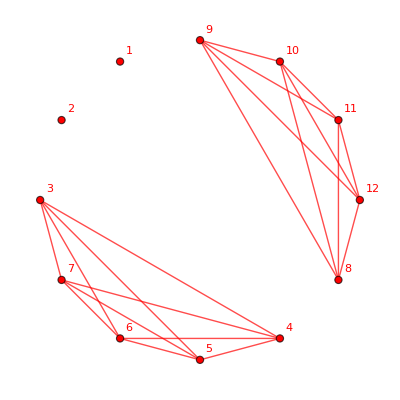
{-Graphics-{9111,0,30,30},-Graphics-{8211,7,30,37},-Graphics-{7311,12,30,42},-Graphics-{7221,13,30,43},-Graphics-{6411,15,30,45},-Graphics-{6321,17,30,47},-Graphics-{6222,18,30,48},-Graphics-{5511,16,30,46},-Graphics-{5421,19,30,49},-Graphics-{5331,20,30,50},-Graphics-{5322,21,30,51},-Graphics-{4431,21,30,51},-Graphics-{4422,22,30,52},-Graphics-{4332,23,30,53},-Graphics-{3333,24,30,54}}

```mathematica
BarelyFourColorableGraphsOfCount2[12]
```

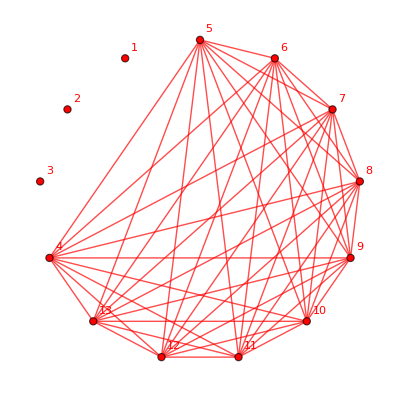
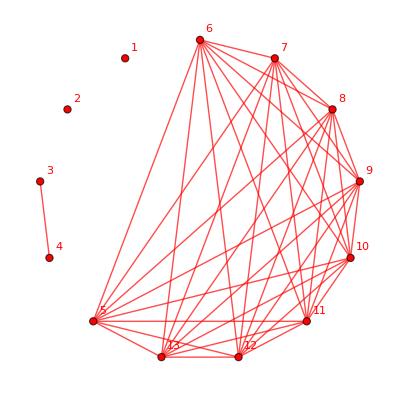
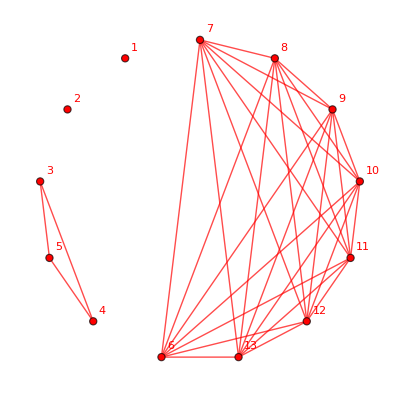
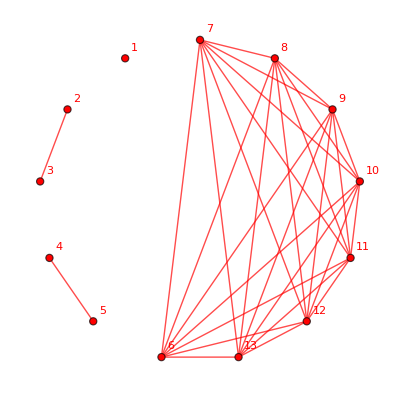
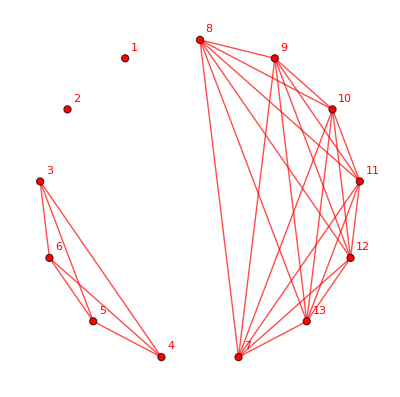
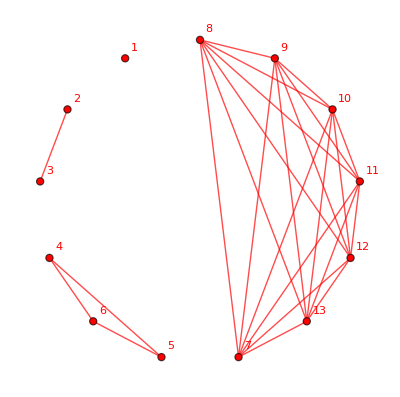
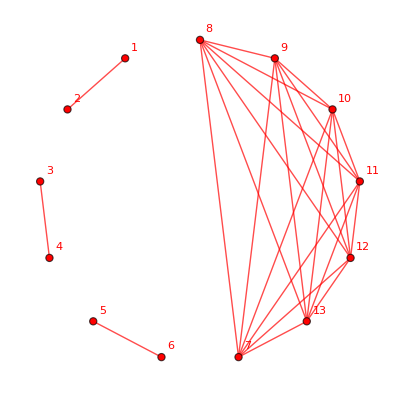
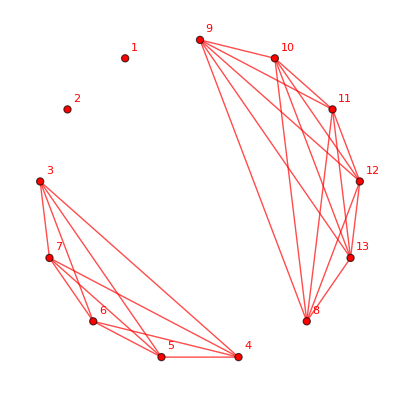
{-Graphics-{10111,0,33,33},-Graphics-{9211,8,33,41},-Graphics-{8311,14,33,47},-Graphics-{8221,15,33,48},-Graphics-{7411,18,33,51},-Graphics-{7321,20,33,53},-Graphics-{7222,21,33,54},-Graphics-{6511,20,33,53},-Graphics-{6421,23,33,56},-Graphics-{6331,24,33,57},-Graphics-{6322,25,33,58},-Graphics-{5521,24,33,57},-Graphics-{5431,26,33,59},-Graphics-{5422,27,33,60},-Graphics-{5332,28,33,61},-Graphics-{4441,27,33,60},-Graphics-{4432,29,33,62},-Graphics-{4333,30,33,63}}

```mathematica
BarelyFourColorableGraphsOfCount2[13]
```

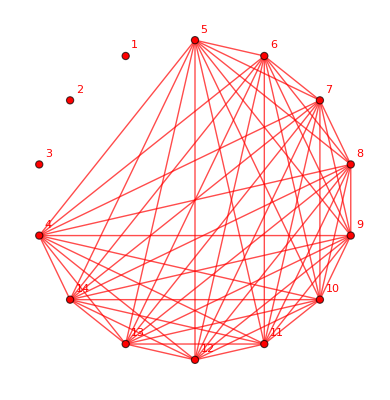
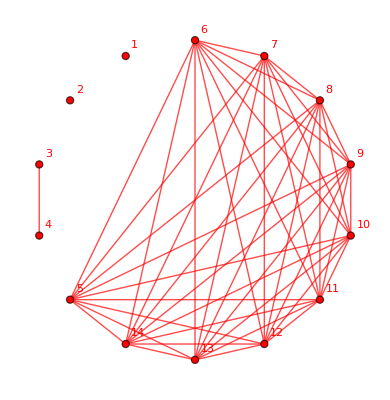
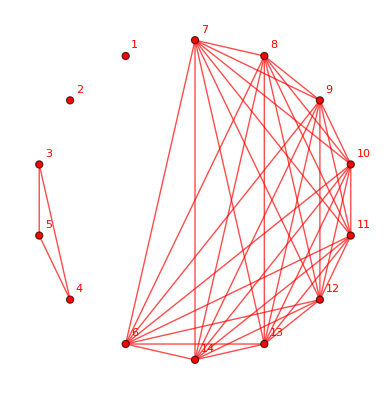
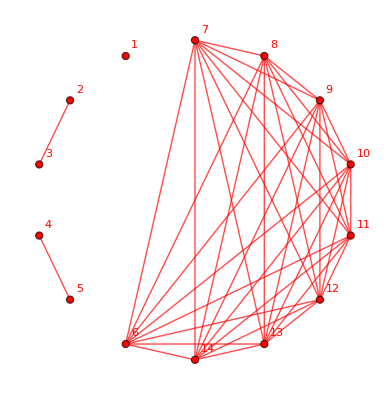
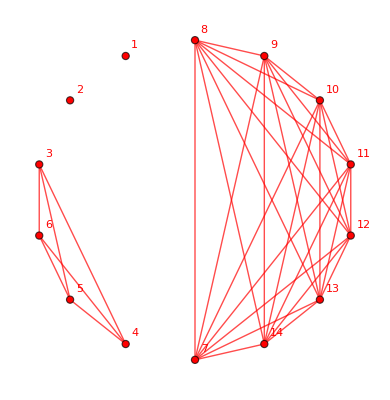
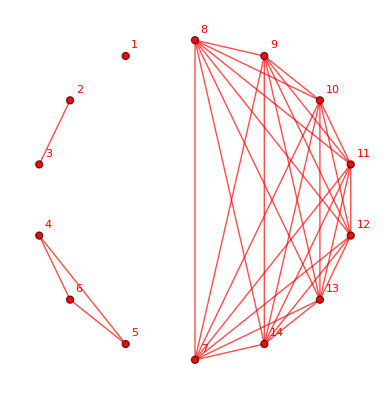
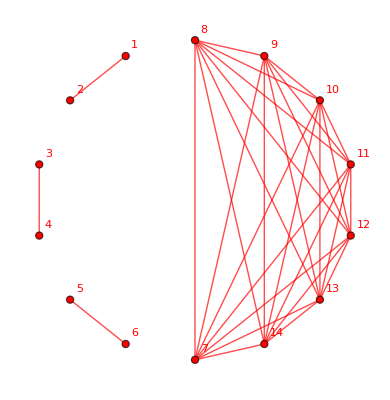
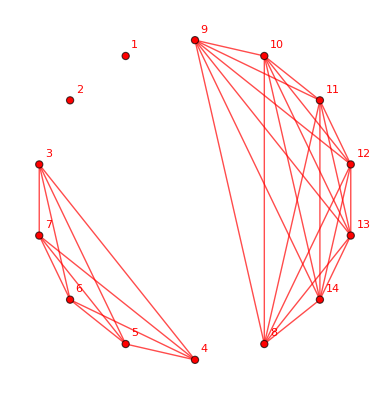
{-Graphics-{11111,0,36,36},-Graphics-{10211,9,36,45},-Graphics-{9311,16,36,52},-Graphics-{9221,17,36,53},-Graphics-{8411,21,36,57},-Graphics-{8321,23,36,59},-Graphics-{8222,24,36,60},-Graphics-{7511,24,36,60},-Graphics-{7421,27,36,63},-Graphics-{7331,28,36,64},-Graphics-{7322,29,36,65},-Graphics-{6611,25,36,61},-Graphics-{6521,29,36,65},-Graphics-{6431,31,36,67},-Graphics-{6422,32,36,68},-Graphics-{6332,33,36,69},-Graphics-{5531,32,36,68},-Graphics-{5522,33,36,69},-Graphics-{5441,33,36,69},-Graphics-{5432,35,36,71},-Graphics-{5333,36,36,72},-Graphics-{4442,36,36,72},-Graphics-{4433,37,36,73}}

```mathematica
BarelyFourColorableGraphsOfCount2[14]
```